```mathematica
(*Data sets for: 2mm, 4mm and 8mm, correspond to the aperature of the lense used to emit an incident light of 436 nm; number pairs are in {voltage, current}*)
```

```mathematica
data2mm = {{-0.93,0},{3.94,85*10^(-11)},{7.95, 124*10^(-11)},{11.91,160*10^(-11)},{15.94, 191*10^(-11)},{19.94,216*10^(-11)},{23.94, 240*10^(-11)},{27.94, 264*10^(-11)},{30.72, 273*10^(-11)}}
```

{{-0.93,0},{3.94,17/20000000000},{7.95,31/25000000000},{11.91,1/625000000},{15.94,191/100000000000},{19.94,27/12500000000},{23.94,3/1250000000},{27.94,33/12500000000},{30.72,273/100000000000}}

```mathematica
data4mm = {{-0.76,0},{2.78,23*10^(-10)},{4.74, 36*10^(-10)},{6.78, 43*10^(-10)},{8.77, 50*10^(-10)},{10.78, 58*10^(-10)},{12.76, 65*10^(-10)},{14.76, 70*10^(-10)},{16.77, 75*10^(-10)},{18.75, 81*10^(-10)}, {22.75, 92*10^(-10)},{26.74, 99*10^(-10)},{30.71, 106*10^(-10)}}
```

{{-0.76,0},{2.78,23/10000000000},{4.74,9/2500000000},{6.78,43/10000000000},{8.77,1/200000000},{10.78,29/5000000000},{12.76,13/2000000000},{14.76,7/1000000000},{16.77,3/400000000},{18.75,81/10000000000},{22.75,23/2500000000},{26.74,99/10000000000},{30.71,53/5000000000}}

```mathematica
data8mm = {{-0.88, 0},{5.87, 156*10^(-10)},{10.9, 240*10^(-10)},{15.87, 300*10^(-10)},{20.86, 354*10^(-10)},{25.89, 411*10^(-10)},{30.72, 445*10^(-10)}}
```

{{-0.88,0},{5.87,39/2500000000},{10.9,3/125000000},{15.87,3/100000000},{20.86,177/5000000000},{25.89,411/10000000000},{30.72,89/2000000000}}

ListPlot::prng: Value of option PlotRange -> {{31 Frame},{(7 Frame)/2500000000}}→True is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

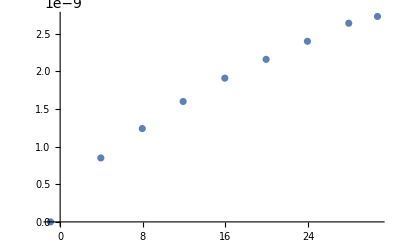

```mathematica
ListPlot[data2mm, PlotRange ->{{31},{280*10^(-11)}} Frame ->True, FrameLabel -> {"Voltage", "Current"}]
```

ListPlot::prng: Value of option PlotRange -> {{31 Frame},{(7 Frame)/2500000000}}→True is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

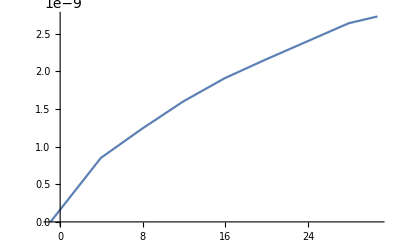

```mathematica
ListPlot[data2mm, PlotRange ->{{31},{280*10^(-11)}} Frame ->True, FrameLabel -> {"Voltage", "Current"}, Joined -> True]
```

```mathematica
Fit[data2mm,{1,x},x]
```

4.54173×10^-10+8.09511×10^-11 x

ListPlot::prng: Value of option PlotRange -> {{31 Frame},{(11 Frame)/1000000000}}→True is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

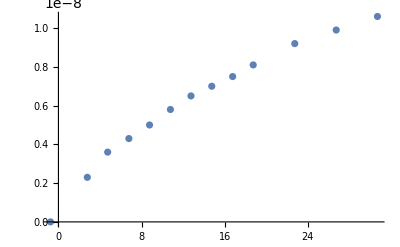

```mathematica
ListPlot[data4mm, PlotRange ->{{31},{110*10^(-10)}} Frame ->True, FrameLabel -> {"Voltage", "Current"}]
```

ListPlot::prng: Value of option PlotRange -> {{31 Frame},{(11 Frame)/1000000000}}→True is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

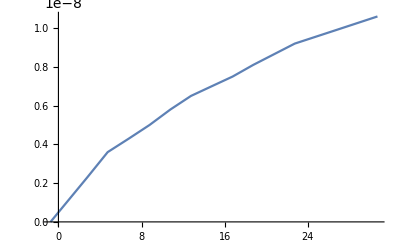

```mathematica
ListPlot[data4mm, PlotRange ->{{31},{110*10^(-10)}} Frame ->True, FrameLabel -> {"Voltage", "Current"}, Joined -> True]
```

```mathematica
Fit[data4mm,{1,x},x]
```

1.37402×10^-9+3.39521×10^-10 x

ListPlot::prng: Value of option PlotRange -> {{31 Frame},{(9 Frame)/200000000}}→True is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

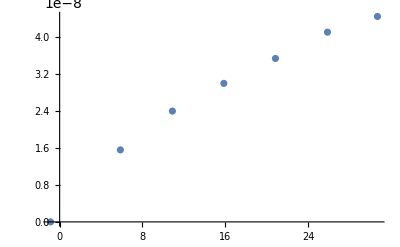

```mathematica
ListPlot[data8mm, PlotRange ->{{31},{450*10^(-10)}} Frame ->True, FrameLabel -> {"Voltage", "Current"}]
```

ListPlot::prng: Value of option PlotRange -> {{31 Frame},{(9 Frame)/200000000}}→True is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

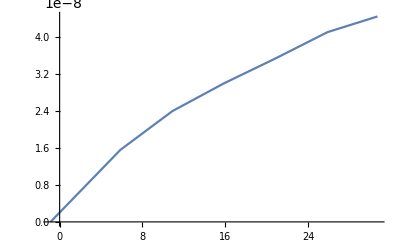

```mathematica
ListPlot[data8mm, PlotRange ->{{31},{450*10^(-10)}} Frame ->True, FrameLabel -> {"Voltage", "Current"}, Joined -> True]
```

```mathematica
Fit[data8mm, {1,x}, x]
```

5.92665×10^-9+1.36513×10^-9 x